```mathematica
(*Quit[]*)
Clear["Global`*"]
```

Antagonistic Specialization Adaptive Dynamics. We begin by defining the change in frequency of each strategist type over time:

```mathematica
(*To begin we first define the payoffs received by hosts and symbionts*)
(*x -> the proportion of a host's resource that is shared*)
(*α -> the matched exchange rate*)
(*αg -> the generalist exchange rate*)
pi=x*(α−x); (*Host matched payoff*)
pi2=x*(fα−x);(*Host mis-matched payoff*)
pig=x*(αg−x);(*Generalist host payoff*)
ψ=x*(1−α);(*Symbiont matched payoff*)
ψ2=x*(1−fα);(*Host mis-matched payoff*)
ψg=x*(1−αg); (*Symbiont payoff from interaction with generalist host*)
```

```mathematica
(*v1 = frequency of host 1*)
(*v2 = frequency of host 2*)
S1 = v1*ψ+v2*ψ2+(1−v1−v2)*ψg;(*Symbiont 1 Average Payoff*)
S2 = v1*ψ2+v2*ψ+(1−v1−v2)*ψg;(*Symbiont 2 Average Payoff*)
S = u*(1-u)*(S1-S2);
S=Simplify[S]; (*Change in Symbiont Frequency over time*)
S/.{v1-> Subscript[v, 1],v2-> Subscript[v, 2],αg-> Subscript[α, g]}
```

-(-1+u) u x (fα-α) (v_1-v_2)

```mathematica
(*u = frequency of symbiont 1*)
H1=u*pi+(1-u)*pi2;(*Host 1 Average Payoff*)
H2 = u*pi2+(1−u)*pi;(*Host 2 Average Payoff*)
HG = pig;(*Generalist Host Average Payoff*)
Hbar = v1*H1+v2*H2+(1-v1-v2)(HG);(*Average payoff of a host selected at random*)
V1=v1*(H1-Hbar);(*Change in Host 1 frequency over time*)
V1=Simplify[V1];
V1/.{v1-> Subscript[v, 1],v2-> Subscript[v, 2],αg-> Subscript[α, g]}
V2=v2(H2-Hbar);(*Change in Host 2 frequency over time*)
V2=Simplify[V2];
V2/.{v1-> Subscript[v, 1],v2-> Subscript[v, 2],αg-> Subscript[α, g]}
```

x v_1 (fα-fα v_1+fα u (-1+v_1-v_2)-α v_2+u α (1-v_1+v_2)-α_g+v_1 α_g+v_2 α_g)

-x v_2 (α (-1+u+u v_1+v_2-u v_2)+fα (v_1+u (-1-v_1+v_2))-(-1+v_1+v_2) α_g)

First we find the equilibria of our system:

Equilibria:

```mathematica
Solve[S==0,u]
Solve[V1 ==0,v1]
Solve[V2 ==0,v2]
```

{{u→0},{u→1}}

{{v1→0},{v1→(-fα+fα u+fα u v2-u α+v2 α-u v2 α+αg-v2 αg)/(-fα+fα u-u α+αg)}}

{{v2→0},{v2→(fα u-fα v1+fα u v1+α-u α-u v1 α-αg+v1 αg)/(fα u+α-u α-αg)}}

Equilibria given as ordered triples: (u, v, p). First boundary Equilibria are the generalist equilibria: (0,0,0) and (1,0,0)

There are other boundary equilibria that occur when a given strategist is absent from the population:

```mathematica
v1s = (-fα+fα u+fα u v2-u α+v2 α-u v2 α+αg-v2 αg)/(-fα+fα u-u α+αg);
v2s = (fα u-fα v1+fα u v1+α-u α-u v1 α-αg+v1 αg)/(fα u+α-u α-αg);
Simplify[v2s /. {u -> 0, v1-> 0}]
Simplify[v2s /. {u -> 1, v1 -> 0}]
Simplify[v1s /. {u -> 0, v2 -> 0}]
Simplify[v1s /. { u -> 1, v2-> 0}]
(*Simplifying a host's internal equilibrium when two strategists are absent reveal additional boundary equilibria*)
```

1

1

1

«1 more identical outputs»

Note the symmetry of these expressions, and that all of them violate our model’s variable constraints by resulting in a host frequency that exceeds 1.

We linearize this system by constructing the jacobian matrix:

```mathematica
J = ({{D[S,u], D[S,v1], D[S,v2]}, {D[V1,u], D[V1,v1], D[V1,v2]}, {D[V2,u], D[V2,v1], D[V2,v2]}});
```

We then evaluate the sign of eigenvalues corresponding to the jacobian evaluated at the boundary equilibria:

Here, we examine the stability of v_1= v_2=0 and u varies.

```mathematica
S/.{v2-> 0, v1-> 0}
V1/.{v2-> 0, v1-> 0}
V2/.{v2-> 0, v1-> 0}
```

0

0

0

Let’s examine the eigenvalues:

```mathematica
Eigenvalues[J/.{v2-> 0, v1-> 0}]
```

{0,x (fα u+α-u α-αg),x (fα-fα u+u α-αg)}

```mathematica
Simplify[H2-pig]
Simplify[H1-pig]
```

x (fα u+α-u α-αg)

x (fα-fα u+u α-αg)

Let’s test its stability using the theory of bifurcation without parameters.

```mathematica
(* Dynamics d[u,v1,v2]/dt = F shifted to the right end point of the interval. This will be the same as the right end point of the interval in cooperative specialization:*)
F={S,V1,V2}/.{u-> u+1-(pi-pig)/(pi-pi2)};
```

```mathematica
(* The Jacobian in the desired form *)
J=Simplify[D[F,{{u,v1,v2}}]/.{u-> 0,v1-> 0,v2->0}]
```

{{0,(x (fα-αg) (-α+αg))/(fα-α),(x (fα-αg) (α-αg))/(fα-α)},{0,0,0},{0,0,x (fα+α-2 αg)}}

```mathematica
(* Reduce system *)
EQ=F/.{u-> μ,v1-> y,v2-> z};
m=a20*μ^2+a11*μ*y+a02*y^2;
IC=D[m,{{μ,y}}].EQ[[1;;2]]-EQ[[3]]/.{z-> m};
```

```mathematica
Q1=Coefficient[IC/.{y->0},μ^2];
Q2=Coefficient[IC,μ*y];
Q3=Coefficient[IC/.{μ->0},y^2];
Solve[{Q1==0,Q2==0,Q3==0},{a11,a02,a20}];
```

```mathematica
(* The reduced system *)
G=Simplify[EQ[[1;;2]]/.{z->0}]
```

{-(x y (fα-αg+fα μ-α μ) (α-αg+fα μ-α μ))/(fα-α),x (-1+y) y (fα-α) μ}

{0.714286 y (-0.6-0.7 μ) (0.1-0.7 μ),-0.35 (-1+y) y μ}

0.857143

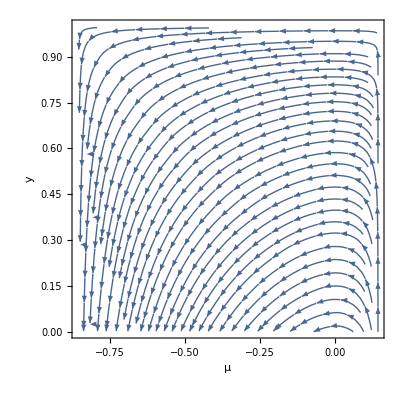

```mathematica
(* Example plotted vector field *)
VF =G/.{α->0.9,fα->0.2,αg->0.8,x->0.5}
(* bifuction point at right endpoint of interval *)
 μ2 = 1-(pi-pig)/(pi-pi2)/.{α->0.9,fα->0.2,αg->0.8,x->0.5} 
StreamPlot[VF[[1;;2]],{μ,-μ2,1-μ2},{y,0,1}, FrameLabel-> {"μ","y"}]
```

While most equilibria were found to violate model parameters when manipulated algebraically,  a sole internal equilibrium at (0.5, 0.5, 0.5) remains. We evaluated the eigenvalues at this point:

```mathematica
Eigenvalues[J/.{u -> 1/2,v1->  1/2,v2-> 1/2} ]/.{v1-> Subscript[v, 1],v2-> Subscript[v, 2],αg-> Subscript[α, g]}
```

{0,0,x (fα+α-2 α_g)}

We used the central limit theorem to evaluate the stability of this internal saddle. We redefine variables so the center ocurs at (0,0,0):

```mathematica
F = {S, V1,V2}/.{v2 -> (v2+1/2), v1 -> (v1+1/2), u -> (u+1/2)}
JC=D[F,{{u,v1,v2}}]/.{u-> 0,v1-> 0,v2-> 0};
```

{-(-1/2+u) (1/2+u) (v1-v2) x (fα-α),(1/2+v1) x (fα-fα (1/2+v1)+fα (1/2+u) (-1+v1-v2)-(1/2+v2) α+(1/2+u) (1-v1+v2) α-αg+(1/2+v1) αg+(1/2+v2) αg),-(1/2+v2) x (fα (1/2+v1+(1/2+u) (-1-v1+v2))+(u+(1/2+u) (1/2+v1)+v2-(1/2+u) (1/2+v2)) α-(v1+v2) αg)}